
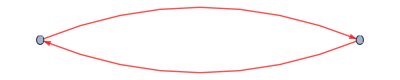
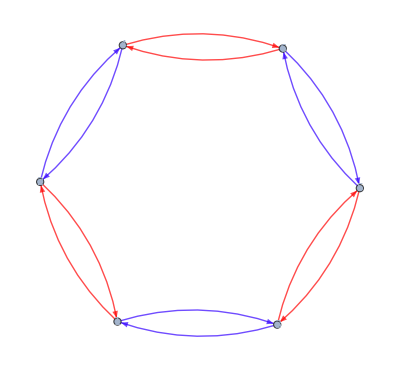
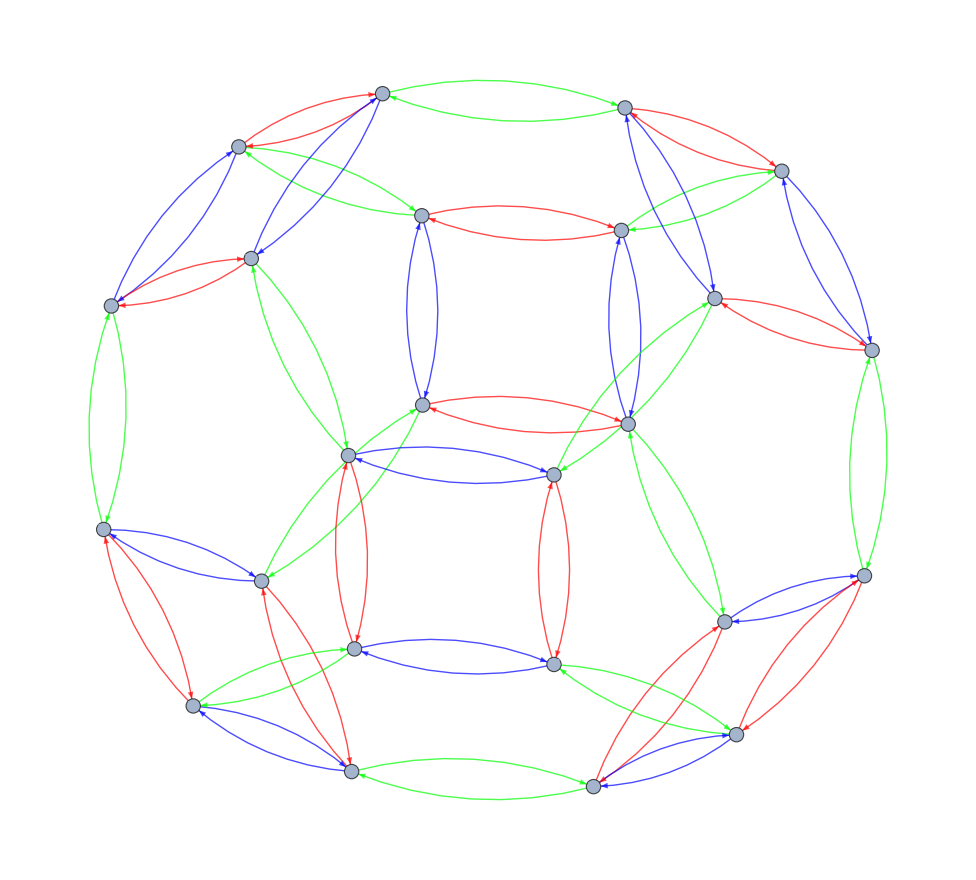
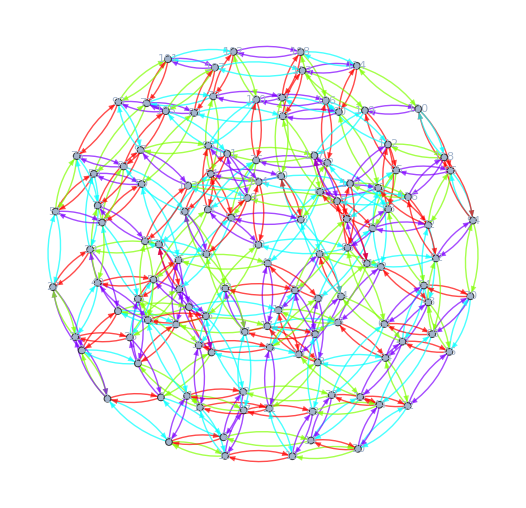
{{-Graphics-,1},{-Graphics-,15},{-Graphics-,25},{-Graphics-,10},{-Graphics-,1}}

```mathematica
Table[CayleyGraph[GraphAutomorphismGroup[allGraphs5[k,"graph"]],VertexLabels->Placed["Name",Center]],{k,allGraphs5AtomKeys}]//Tally//Sort
```

```mathematica
Test[kkk_]:=GroupOrder[GraphAutomorphismGroup[allGraphs5[kkk,"graph"]]]
```

```mathematica
With[{m=0},
Test[0]-> Table[Table[Test[child],{child,c}],{c,allGraphs5[m,"children"]}]
]
```

120→{{12,24},{12,24},{12,24},{12,24},{12,24},{12,24},{12,24},{12,24},{12,24},{12,24}}

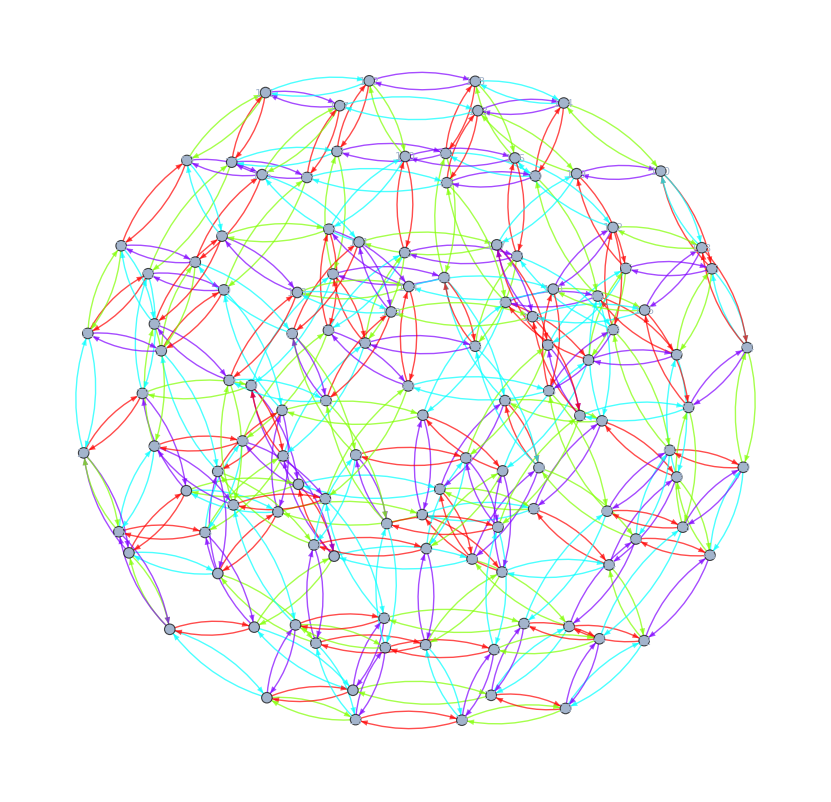
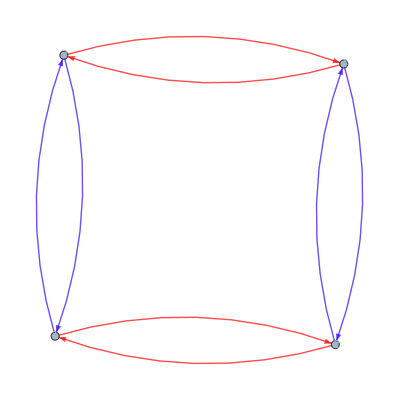
-Graphics-→{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
With[{m=alfaKey},
Test[0]-> Table[Table[Test[child],{child,c}],{c,allGraphs5[m,"children"]}]
]
```

```mathematica
CayleyGraph[PermutationGroup[{Cycles[{{2,3},{4,5}}],Cycles[{{1,2},{3,5}}]}]]
```

-Graphics-

```mathematica
Sort[Tally[Table[Test[k],{k,Keys[allGraphs5]}]],#1[[2]]<#2[[2]]&]
```

{{1,1},{120,2},{10,12},{24,30},{12,60},{8,120},{6,170},{4,300},{2,1200}}

```mathematica
Map[ShowGraph5Least,Select[Keys[allGraphs5],Test[#]==10&]]
```

{-Graphics-263294,-Graphics-262814,-Graphics-221174,-Graphics-219094,-Graphics-206653,-Graphics-205054,-Graphics-90194,-Graphics-88595,-Graphics-76154,-Graphics-74074,-Graphics-32434,-Graphics-31954}

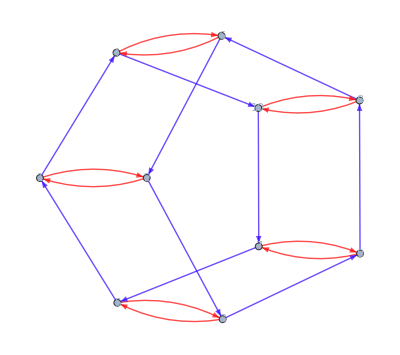
```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[Test[#],-Graphics-]&]
```

{26281,20665}

```mathematica
ShowGraph5Least[26281]
```

-Graphics-262814

```mathematica
ShowGraph5Least[20665]
```

-Graphics-206653

```mathematica
IsomorphicGraphQ[allGraphs5[26281,"graph"],allGraphs5[20505,"graph"]]
```

True

```mathematica
Table[GraphAutomorphismGroup[allGraphs5[k,"graph"]],{k,{26281,20505}}]
```

{PermutationGroup[{Cycles[{{2,3},{4,5}}],Cycles[{{1,2,5,4,3}}]}],PermutationGroup[{Cycles[{{2,5},{3,4}}],Cycles[{{1,2},{4,5}}]}]}

```mathematica
Table[ShowGraph5Least[k]->Test[k],{k,Select[Keys[allGraphs5],IsomorphicGraphQ[allGraphs5[#,"graph"],allGraphs5[lambdaKey,"graph"]]&]}]
```

{-Graphics-263294→-Graphics-,-Graphics-262814→-Graphics-,-Graphics-221174→-Graphics-,-Graphics-219094→-Graphics-,-Graphics-206653→-Graphics-,-Graphics-205054→-Graphics-,-Graphics-90194→-Graphics-,-Graphics-88595→-Graphics-,-Graphics-76154→-Graphics-,-Graphics-74074→-Graphics-,-Graphics-32434→-Graphics-,-Graphics-31954→-Graphics-}

```mathematica
Test[starKey]
```

-Graphics-

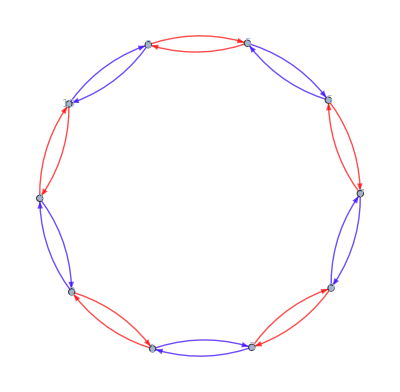
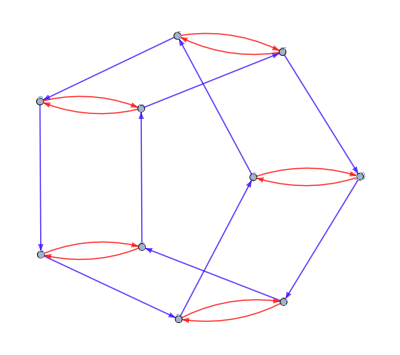
```mathematica
FindGraphIsomorphism[-Graphics-,-Graphics-]
```

{}